# Test Neuralynx IO

These tests require the standard test file resources folder to be downloaded from Git and available at Tests/_resources.

Updated 2015.12 .31

```mathematica
<<NounouW`
```

HokahokaW`HHPackageGitLoad: Loaded Git repository located at C:\prog\_w\HokahokaW\.git

HokahokaW`
Tue 12 Jan 2016 11:58:14     [Mathematica: 10.3.1 for Microsoft Windows (64-bit) (December 9, 2015)]
     Current local repository path:   C:\prog\_w\HokahokaW\.git
     Current branch [hash]:  dev [49d44a08c64a146a010f8de46223ecea3699dedd]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/HokahokaW.git)

<<Set JLink` java stack size to 6144Mb>>

Unloading repository: C:\prog\_w\HokahokaW\.git

HokahokaW`HHPackageGitLoad: Loaded Git repository located at C:\prog\_w\NounouW\.git

NounouW`
Tue 12 Jan 2016 11:58:16     [Mathematica: 10.3.1 for Microsoft Windows (64-bit) (December 9, 2015)]
     Current local repository path:   C:\prog\_w\NounouW\.git
     Current branch [hash]:  dev [2c919269f4d06d25ee73b3e07c732c110d1d4ea1]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/NounouW.git)

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 3cc31723ae141d3f2622c7f26ab9e5a96b19674c
  + current branch is: master
  + remote names are: https://ktakagaki@github.com/ktakagaki/nounou.git

```mathematica
{resourceDataDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]], "_resources","nounou","Neuralynx"}] ,
FileExistsQ[resourceDataDirectory]}//Column
```

C:\prog\_w\NounouW\NounouW\Tests\_resources\nounou\Neuralynx
True

```mathematica
(*ShowJavaConsole[]*)
```

## NCS1 (SPP010: single channel, many segments)

```mathematica
testNCS1 = NNLoad[ FileNameJoin[{resourceDataDirectory,"SPP010","2013-12-02_17-07-31",#}]& /@{"Tet4a.ncs","Tet4b.ncs","Tet4c.ncs","Tet4d.ncs"} ]
```

«JavaObject[nounou.elements.data.NNDataChannelArray]»

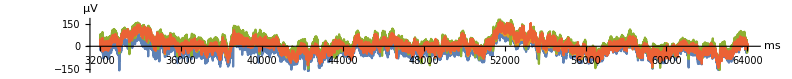

```mathematica
NNTracePlot[testNCS1, All, { 32001;;64000,0}, AspectRatio-> 1/10, ImageSize->11*72, NNOptStack-> None]
```

### Timing information

```mathematica
testNCS1@getTiming[]@toString[]
```

NNTiming(fs=32000.0, segmentCount=1)

```mathematica
NNPrintInfo[testNCS1]
```

nounou.elements.data.NNDataChannelArray(1 segments, fs=32000.0,  , 1a58c41332)
NNTiming(fs=32000.0, segmentCount=1)

NNDataChannelArray(1 segments, fs=32000.0,

```mathematica
NNPrintInfo[testNCS1, "Timing"](*testNCS1@getTiming[]@toStringFull[]*)
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
================================================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	 151597056 ( 78:57.41) (  4737.4)	 19228868023 ( 0:00.00)

## NCS1 (E04LC: single channel, many segments)

```mathematica
testNCS1 = NNLoad[ FileNameJoin[{resourceDataDirectory,"E04LC","CSC1.ncs"}] ]
```

«JavaObject[nounou.io.neuralynx.NNDataChannelFileReadNCS]»

### Timing information

```mathematica
testNCS1@getTiming[]@toString[]
```

NNTiming(fs=32000.0, segmentCount=94)

```mathematica
NNPrintInfo[testNCS1]
```

nounou.io.neuralynx.NNDataChannelFileReadNCS(94 segments, fs=32000.0file=C:\prog\_w\NounouW\NounouW\Tests\_resources\nounou\Neuralynx\E04LC\CSC1.ncs, , 3cc31723ae)

```mathematica
NNPrintInfo[testNCS1, "Timing"](*testNCS1@getTiming[]@toStringFull[]*)
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=94, 3cc31723ae)
================================================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	   2546176 (  1:19.57) (    79.6)	 10237373715 ( 0:00.00)
   1	   2170880 (  1:07.84) (    67.8)	 10664246433 ( 0:07.11)
   2	   2305024 (  1:12.03) (    72.0)	 10754520433 ( 0:08.62)
   3	   2161664 (  1:07.55) (    67.6)	 10850792433 ( 0:10.22)
   4	   2997760 (  1:33.68) (    93.7)	 11295017433 ( 0:17.63)
   5	   2387456 (  1:14.61) (    74.6)	 11487036433 ( 0:20.83)
   6	   2265088 (  1:10.78) (    70.8)	 11583691433 ( 0:22.44)
   7	   2387456 (  1:14.61) (    74.6)	 11683016433 ( 0:24.09)
   8	   3902976 (  2:01.97) (   122.0)	 11827213433 ( 0:26.50)
   9	   2618368 (  1:21.82) (    81.8)	 11983645433 ( 0:29.10)
  10	   1647104 (  0:51.47) (    51.5)	 12072502433 ( 0:30.59)
  11	   1575424 (  0:49.23) (    49.2)	 12133227433 ( 0:31.60)
  12	   3245056 (  1:41.41) (   101.4)	 12288900433 ( 0:34.19)
  13	   2422784 (  1:15.71) (    75.7)	 12409026433 ( 0:36.19)
  14	   2198528 (  1:08.70) (    68.7)	 12498511433 ( 0:37.69)
  15	   2352128 (  1:13.50) (    73.5)	 12579166433 ( 0:39.03)
  16	   2157568 (  1:07.42) (    67.4)	 12741121433 ( 0:41.73)
  17	   2134528 (  1:06.70) (    66.7)	 12858472433 ( 0:43.68)
  18	   2119680 (  1:06.24) (    66.2)	 12936583433 ( 0:44.99)
  19	   2090496 (  1:05.33) (    65.3)	 13017220433 ( 0:46.33)
  20	   2553344 (  1:19.79) (    79.8)	 13093848433 ( 0:47.61)
  21	   1839616 (  0:57.49) (    57.5)	 16591907433 ( 1:45.91)
  22	   1851392 (  0:57.86) (    57.9)	 16672397433 ( 1:47.25)
  23	   1785344 (  0:55.79) (    55.8)	 16753078433 ( 1:48.60)
  24	   1777152 (  0:55.54) (    55.5)	 16830068433 ( 1:49.88)
  25	   2441216 (  1:16.29) (    76.3)	 16973050433 ( 1:52.26)
  26	   1899520 (  0:59.36) (    59.4)	 21828657152 ( 3:13.19)
  27	   1888256 (  0:59.01) (    59.0)	 21913112152 ( 3:14.60)
  28	   1721856 (  0:53.81) (    53.8)	 21991295152 ( 3:15.90)
  29	   1846784 (  0:57.71) (    57.7)	 22066384152 ( 3:17.15)
  30	   2132992 (  1:06.66) (    66.7)	 22160886152 ( 3:18.73)
  31	   2460160 (  1:16.88) (    76.9)	 22251741152 ( 3:20.24)
  32	   2265088 (  1:10.78) (    70.8)	 22352221152 ( 3:21.91)
  33	   2185216 (  1:08.29) (    68.3)	 22445370152 ( 3:23.47)
  34	   3800064 (  1:58.75) (   118.8)	 22580373152 ( 3:25.72)
  35	   2446848 (  1:16.46) (    76.5)	 22705666152 ( 3:27.80)
  36	   1822208 (  0:56.94) (    56.9)	 22805853152 ( 3:29.47)
  37	   1444352 (  0:45.14) (    45.1)	 22870118152 ( 3:30.55)
  38	   2193920 (  1:08.56) (    68.6)	 22968881152 ( 3:32.19)
  39	   2121728 (  1:06.30) (    66.3)	 23062296152 ( 3:33.75)
  40	   2095104 (  1:05.47) (    65.5)	 23137807152 ( 3:35.01)
  41	   2156544 (  1:07.39) (    67.4)	 23280546152 ( 3:37.39)
  42	   2127360 (  1:06.48) (    66.5)	 23370970152 ( 3:38.89)
  43	   2094592 (  1:05.46) (    65.5)	 23438460152 ( 3:40.02)
  44	   2126848 (  1:06.46) (    66.5)	 23504925152 ( 3:41.13)
  45	   2122240 (  1:06.32) (    66.3)	 23573260152 ( 3:42.26)
  46	   1861632 (  0:58.18) (    58.2)	 23863261152 ( 3:47.10)
  47	   1770496 (  0:55.33) (    55.3)	 23940017152 ( 3:48.38)
  48	   1795584 (  0:56.11) (    56.1)	 24017170152 ( 3:49.66)
  49	   1971712 (  1:01.62) (    61.6)	 24107429152 ( 3:51.17)
  50	   2276352 (  1:11.14) (    71.1)	 24266402152 ( 3:53.82)
  51	   2361344 (  1:13.79) (    73.8)	 24363959152 ( 3:55.44)
  52	   2138624 (  1:06.83) (    66.8)	 24457818152 ( 3:57.01)
  53	   2222592 (  1:09.46) (    69.5)	 24540062152 ( 3:58.38)
  54	   3304448 (  1:43.26) (   103.3)	 24660860152 ( 4:00.39)
  55	   2171904 (  1:07.87) (    67.9)	 24773138152 ( 4:02.26)
  56	   1558528 (  0:48.70) (    48.7)	 24847063152 ( 4:03.49)
  57	   1312256 (  0:41.01) (    41.0)	 24901897152 ( 4:04.41)
  58	   3031040 (  1:34.72) (    94.7)	 24986583152 ( 4:05.82)
  59	   2152448 (  1:07.26) (    67.3)	 25092888152 ( 4:07.59)
  60	   2109440 (  1:05.92) (    65.9)	 25161343152 ( 4:08.73)
  61	   2138112 (  1:06.82) (    66.8)	 25227916152 ( 4:09.84)
  62	   2124800 (  1:06.40) (    66.4)	 25306723152 ( 4:11.16)
  63	   2082816 (  1:05.09) (    65.1)	 25374354152 ( 4:12.28)
  64	   2061312 (  1:04.42) (    64.4)	 25440636152 ( 4:13.39)
  65	   2149888 (  1:07.18) (    67.2)	 25506334152 ( 4:14.48)
  66	   1409024 (  0:44.03) (    44.0)	 25618653152 ( 4:16.35)
  67	   1364992 (  0:42.66) (    42.7)	 25686018152 ( 4:17.48)
  68	   1436672 (  0:44.90) (    44.9)	 25749984152 ( 4:18.54)
  69	   1519104 (  0:47.47) (    47.5)	 25813278152 ( 4:19.60)
  70	   1218560 (  0:38.08) (    38.1)	 26345811152 ( 4:28.47)
  71	   1157632 (  0:36.18) (    36.2)	 26401763152 ( 4:29.41)
  72	   1254912 (  0:39.22) (    39.2)	 26454942152 ( 4:30.29)
  73	   1192960 (  0:37.28) (    37.3)	 26520656152 ( 4:31.39)
  74	    817152 (  0:25.54) (    25.5)	 26628123152 ( 4:33.18)
  75	    733696 (  0:22.93) (    22.9)	 26676913152 ( 4:33.99)
  76	    558592 (  0:17.46) (    17.5)	 26716100152 ( 4:34.65)
  77	    545280 (  0:17.04) (    17.0)	 26745031152 ( 4:35.13)
  78	    700928 (  0:21.90) (    21.9)	 26784193152 ( 4:35.78)
  79	    702976 (  0:21.97) (    22.0)	 26819927152 ( 4:36.38)
  80	    757248 (  0:23.66) (    23.7)	 26866787152 ( 4:37.16)
  81	    644096 (  0:20.13) (    20.1)	 26903901152 ( 4:37.78)
  82	    769024 (  0:24.03) (    24.0)	 27119440152 ( 4:41.37)
  83	    592896 (  0:18.53) (    18.5)	 27165321152 ( 4:42.13)
  84	   1137664 (  0:35.55) (    35.6)	 27199194152 ( 4:42.70)
  85	    961024 (  0:30.03) (    30.0)	 27247322152 ( 4:43.50)
  86	    455680 (  0:14.24) (    14.2)	 27298550152 ( 4:44.35)
  87	    493568 (  0:15.42) (    15.4)	 27324852152 ( 4:44.79)
  88	    471552 (  0:14.74) (    14.7)	 27354092152 ( 4:45.28)
  89	    418816 (  0:13.09) (    13.1)	 27382802152 ( 4:45.76)
  90	    388608 (  0:12.14) (    12.1)	 27415682152 ( 4:46.31)
  91	    386560 (  0:12.08) (    12.1)	 27440979152 ( 4:46.73)
  92	    370176 (  0:11.57) (    11.6)	 27468094152 ( 4:47.18)
  93	    368640 (  0:11.52) (    11.5)	 27488855152 ( 4:47.52)

### Specifying time ranges

```mathematica
testRange=$NNSpanToNNRangeSpecifier[ {10 ;; 20, 0}];
{testRange, NNReadTimepoints[ testRange, testNCS1 ]}
```

{«JavaObject[nounou.ranges.NNRange]»,{10,11,12,13,14,15,16,17,18,19,20}}

```mathematica
testRange=$NNSpanToNNRangeSpecifier[ {10 ;; 20 ;;5, 2}];
{testRange, NNReadTimepoints[ testRange, testNCS1 ]}
```

{«JavaObject[nounou.ranges.NNRange]»,{10,15,20}}

```mathematica
testRange@segment[]
```

2

```mathematica
Remove[$NNSpanToNNRangeSpecifier]
```

```mathematica
testRange=$NNSpanToNNRangeSpecifier[ 10237373715 -> 0;; 10];
{testRange, NNReadTimepoints[ testRange, testNCS1 ]}
```

{«JavaObject[nounou.ranges.NNRangeTsEvent]»,{10237373715,10237373746,10237373778,10237373809,10237373840,10237373871,10237373903,10237373934,10237373965,10237373996,10237374028}}

```mathematica
testRange=$NNSpanToNNRangeSpecifier[ {10237373715, 10238373715} -> 0;; 10];
{testRange, NNReadTimepoints[ #, testNCS1 ]& /@ testRange}
```

{{«JavaObject[nounou.ranges.NNRangeTsEvent]»,«JavaObject[nounou.ranges.NNRangeTsEvent]»},{{10237373715,10237373746,10237373778,10237373809,10237373840,10237373871,10237373903,10237373934,10237373965,10237373996,10237374028},{10238373715,10238373746,10238373778,10238373809,10238373840,10238373871,10238373903,10238373934,10238373965,10238373996,10238374028}}}

### NNReadTrace

```mathematica
testData=NNReadTrace[testNCS1,{ 32001;;64000,0} ];
```

```mathematica
ListLinePlot[testData, AspectRatio-> 1/10, ImageSize->11*72]//Rasterize
```

-Graphics-

### NNDataDownsample

```mathematica
testNCS1Downsample = NNDataDownsample[testNCS1, 8]
```

«JavaObject[nounou.elements.data.NNDataChannelExtracted]»

```mathematica
NNPrintInfo[ testNCS1Downsample ]
```

nounou.elements.data.NNDataChannelExtracted(94 segments, fs=4000.0, 3cc31723ae)

```mathematica
testDataFiltered = NNReadTrace[testNCS1Downsample,{ 4001;;8000,0} ];
```

```mathematica
ListLinePlot[testDataFiltered, AspectRatio-> 1/10, ImageSize->11*72]//Rasterize
```

-Graphics-

### NNDataDecimate

```mathematica
testNCS1Decimate = NNDataDecimate[testNCS1, 8]
```

«JavaObject[nounou.elements.data.NNDataChannelExtracted]»

```mathematica
NNPrintInfo[ testNCS1Decimate ]
```

nounou.elements.data.NNDataChannelExtracted(94 segments, fs=4000.0, 3cc31723ae)

```mathematica
testDataFiltered = NNReadTrace[testNCS1Decimate,{ 4001;;8000,0} ];
```

```mathematica
ListLinePlot[testDataFiltered, AspectRatio-> 1/10, ImageSize->11*72]//Rasterize
```

-Graphics-

### Whole Range Plot

## NEV

```mathematica
testNEV1 = NNLoad[ FileNameJoin[{resourceDataDirectory,"t130911","Events.nev"}] ]
```

«JavaObject[nounou.elements.events.NNEvents]»

```mathematica
testNEV1@toString[]
```

NNEvents(ports=2, events=List(5, 2702))

```mathematica
NNPrintInfo[testNEV1]
```

nounou.elements.events.NNEvents(ports=2, events=List(5, 2702), 3cc31723ae)
================================================================================
Port 0
    Code     0 (00000000):        5 eventsPort 1000001
    Code     1 (00000001):      246 events
    Code     2 (00000010):      232 events
    Code     3 (00000011):      260 events
    Code     4 (00000100):      232 events
    Code     5 (00000101):      241 events
    Code     6 (00000110):      268 events
    Code     7 (00000111):      240 events
    Code     8 (00001000):      238 events
    Code     9 (00001001):      250 events
    Code    10 (00001010):      241 events
    Code    11 (00001011):      254 events

```mathematica
NNReadEvents[testNEV1, "Ports"]
```

{0,1000001}

```mathematica
NNReadEvents[testNEV1, 1000001][[1;;15]]//Table
```

{{{21412881115,203562},1,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).},{{21413605959,204312},8,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).},{{21414493771,204156},6,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).},{{21415235771,204344},5,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).},{{21415969271,204219},11,TTL Input on AcqSystem1_0 board 0 port 1 value (0x000B).},{{21416703521,204438},3,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).},{{21417397021,204219},8,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).},{{21418214365,204219},11,TTL Input on AcqSystem1_0 board 0 port 1 value (0x000B).},{{21418880240,204406},9,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).},{{21419581521,203281},8,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).},{{21420529646,204344},6,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).},{{21421163552,204219},3,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).},{{21422121552,204344},5,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).},{{21422655302,203719},7,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).},{{21423563084,204156},2,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).}}